```mathematica
(*Using Zhu, Xiong paper*)
(* Distance between nuclei*)

(**)

(* Solve the separated equation in 2D *)
(* L equation and coefficients *)
σ[r_]:=r/p-1/2;
α[n_]:=(n+1)(n+1/2);
β[n_,r_]:=2 n^2+(4p-2σ[r])n-A +p^2-2p σ[r]-σ[r]/2;
γ[n_,r_]:=(n-1)(n-2σ[r]-1/2)+σ[r](σ[r]-1/2);

(* Create a continued fraction equation for the coefficients of L equation *)

lCoeff2[n_,r_]:=β[0,r]/α[0]+Simplify[ContinuedFractionK[-α[i-1]γ[i,r],β[i,r],{i,1,n}]] ;

(* M equation and coefficients *)

w=-A +p^2/2;      q= -p^2/4;
v[n_]:=(w-n^2)/q;
(* Evaluate as a continued fraction *)
mCoeffV0[n_]:=v[0]+2Simplify[ContinuedFractionK[-1,v[2i],{i,1,n}]];

mCoeffV1[n_]:=v[1]-1+Simplify[ContinuedFractionK[-1,v[2i+1],{i,1,n}]];

(* Compute the eigenvalue, i.e. the energy for the single value of R .
R - internuclear separation *)
(* Parameters:
n: Depth of the continued fraction,
 R: Internuclear distance,
 gerade: flag indicating whether we are calculating gerade or ungerade states
output:
R , electron energy, total energy, separation constant, and p value 
*)
energySingleR[n_,R_, gerade_]:=
Module[{asAndps,pe,energy,aa},
(*Now find p and A *)
If[gerade==1, 
asAndps= NSolve[{lCoeff2[n,R]==0,
mCoeffV0[n]==0},{A,p},Reals],
asAndps= NSolve[{lCoeff2[n,R]==0,
mCoeffV1[n]==0},{A,p},Reals]];
aa=Sort[asAndps[[All,1,2]], Greater][[1]];
pe=Sort[asAndps[[All,2,2]], Greater][[1]];
energy = (-2)/R^2 pe^2;
{R,energy, energy + 1/R,aa,pe}
]
allRs = {0.1};
allRs = Join[allRs,Table[0.2+i*0.1,{i,0,9}]];
allRs = Join[allRs, Table[1+.5*i,{i,1,8}]];
allRs = Join[allRs, Table[5+i,{i,1,55}]];

energiesGerade1S = Map[energySingleR[9,#1,1] &, allRs];
energiesUngerade1S = Map[energySingleR[9,#1,2] &, allRs];

(*
Prepend[energiesGerade1S, {"R", "E", "E+1/r", "A", "p"}]  ;
Prepend[energiesUngerade1S, {"R", "E", "E+1/r", "A", "p"}]  ;
*)

Print["Gerade"];
energiesGerade1S //MatrixForm
Print["UnGerade"];
energiesUngerade1S//MatrixForm

grid=Transpose@{energiesGerade1S[[All,1]],energiesGerade1S[[All,3]],energiesUngerade1S[[All,3]],energiesGerade1S[[All,3]]- energiesUngerade1S[[All,3]]};
grid // MatrixForm
```

Gerade

(0.1 | -7.33546 | 2.66454 | 25.1435 | 0.191513
0.2 | -6.50327 | -1.50327 | 25.2156 | 0.360646
0.3 | -5.81972 | -2.48638 | 25.2874 | 0.511749
0.4 | -5.27548 | -2.77548 | 49.1533 | 0.649645
0.5 | -4.8382 | -2.8382 | 49.2354 | 0.777673
0.6 | -4.48148 | -2.81481 | 232.663 | 0.898146
0.7 | -4.18616 | -2.75759 | 49.3992 | 1.01272
0.8 | -3.93852 | -2.68852 | 251.243 | 1.12264
0.9 | -3.72861 | -2.61749 | 259.428 | 1.22886
1. | -3.54904 | -2.54904 | 267.061 | 1.33211
1.1 | -3.39429 | -2.4852 | 1533.02 | 1.43302
1.5 | -2.95083 | -2.28416 | 299.501 | 1.822
2. | -2.63638 | -2.13638 | 325.943 | 2.29625
2.5 | -2.4621 | -2.0621 | 782.819 | 2.77382
3. | -2.36086 | -2.02753 | 369.172 | 3.25943
3.5 | -2.29798 | -2.01226 | 387.773 | 3.75168
4. | -2.25568 | -2.00568 | 404.996 | 4.24799
4.5 | -2.22506 | -2.00284 | 938.279 | 4.74644
5. | -2.20156 | -2.00156 | 436.346 | 5.24591
6 | -2.16732 | -2.00065 | 134374. | 6.24594
7 | -2.14322 | -2.00036 | 22390.3 | 7.2463
8 | -2.12523 | -2.00023 | 134514. | 8.24666
9 | -2.11127 | -2.00016 | 643473. | 9.24697
10 | -2.10012 | -2.00012 | 134654. | 10.2472
11 | -2.091 | -2.00009 | 644774. | 11.2475
12 | -2.0834 | -2.00007 | 134794. | 12.2476
13 | -2.07698 | -2.00005 | 192643. | 13.2478
14 | -2.07147 | -2.00004 | 87195. | 14.2479
15 | -2.0667 | -2.00003 | 22578.8 | 15.2481
16 | -2.06253 | -2.00003 | 135073. | 16.2482
17 | -2.05885 | -2.00002 | 30904.3 | 17.2483
18 | -2.05557 | -2.00002 | 135212. | 18.2484
19 | -2.05265 | -2.00002 | 22672.7 | 19.2485
20 | -2.05001 | -2.00001 | 87616.2 | 20.2485
21 | -2.04763 | -2.00001 | 49987.5 | 21.2486
22 | -2.04546 | -2.00001 | 135491. | 22.2486
23 | -2.04349 | -2.00001 | 22766.5 | 23.2487
24 | -2.04167 | -2.00001 | 87896.4 | 24.2487
25 | -2.04 | -2. | 31090.6 | 25.2488
26 | -2.03846 | -2. | 135769. | 26.2488
27 | -2.03703 | -1.99999 | 31137.1 | 27.2488
28 | -2.0357 | -1.99999 | 135909. | 28.2488
29 | -2.03446 | -1.99998 | 135978. | 29.2488
30 | -2.0333 | -1.99996 | 136048. | 30.2487
31 | -2.0322 | -1.99995 | 31229.9 | 31.2486
32 | -2.03117 | -1.99992 | 136187. | 32.2484
33 | -2.03019 | -1.99989 | 194032. | 33.2482
34 | -2.02926 | -1.99985 | 136326. | 34.2478
35 | -2.02836 | -1.99979 | 50976.5 | 35.2473
36 | -2.0275 | -1.99973 | 136464. | 36.2467
37 | -2.02667 | -1.99964 | 4.43239×10^6 | 37.2459
38 | -2.02585 | -1.99954 | 136603. | 38.2448
39 | -2.02505 | -1.99941 | 194447. | 39.2435
40 | -2.02426 | -1.99926 | 136742. | 40.2419
41 | -2.02347 | -1.99908 | 23748.7 | 41.2399
42 | -2.02268 | -1.99887 | 136880. | 42.2375
43 | -2.02189 | -1.99863 | 4.43626×10^6 | 43.2346
44 | -2.02107 | -1.99835 | 137019. | 44.2312
45 | -2.02024 | -1.99802 | 24032.9 | 45.2272
46 | -2.01939 | -1.99765 | 137158. | 46.2225
47 | -2.01851 | -1.99723 | 4.43884×10^6 | 47.217
48 | -2.0176 | -1.99676 | 137296. | 48.2107
49 | -2.01665 | -1.99624 | 4.44013×10^6 | 49.2035
50 | -2.01565 | -1.99565 | 137434. | 50.1953)

UnGerade

(0.1 | -0.809375 | 9.19063 | 25.1425 | 0.0636151
0.2 | -0.84131 | 4.15869 | 25.2145 | 0.129716
0.3 | -0.911853 | 2.42148 | 49.0709 | 0.202567
0.4 | -1.03325 | 1.46675 | 270.257 | 0.287506
0.5 | -1.20116 | 0.798836 | 630.315 | 0.387486
0.6 | -1.39268 | 0.273983 | 657.607 | 0.500683
0.7 | -1.58213 | -0.153558 | 682.09 | 0.622593
0.8 | -1.75267 | -0.502669 | 704.426 | 0.748902
0.9 | -1.89725 | -0.786143 | 725.059 | 0.876577
1. | -2.01521 | -1.01521 | 744.303 | 1.0038
1.1 | -2.10899 | -1.1999 | 762.388 | 1.12957
1.5 | -2.31161 | -1.64494 | 826.127 | 1.61262
2. | -2.36744 | -1.86744 | 892.852 | 2.17598
2.5 | -2.35029 | -1.95029 | 950.496 | 2.7101
3. | -2.31526 | -1.98193 | 2466.98 | 3.2278
3.5 | -2.2797 | -1.99399 | 2592.96 | 3.73673
4. | -2.24845 | -1.99845 | 2710.09 | 4.24118
4.5 | -2.22223 | -2. | 2820.12 | 4.74342
5. | -2.20046 | -2.00046 | 5850.68 | 5.2446
6 | -2.16715 | -2.00049 | 27434. | 6.2457
7 | -2.1432 | -2.00034 | 27460.3 | 7.24626
8 | -2.12523 | -2.00023 | 27486.7 | 8.24666
9 | -2.11127 | -2.00016 | 27513. | 9.24697
10 | -2.10012 | -2.00012 | 27539.4 | 10.2472
11 | -2.091 | -2.00009 | 27565.7 | 11.2475
12 | -2.0834 | -2.00007 | 164271. | 12.2476
13 | -2.07698 | -2.00005 | 27618.2 | 13.2478
14 | -2.07147 | -2.00004 | 60244.3 | 14.2479
15 | -2.0667 | -2.00003 | 27670.8 | 15.2481
16 | -2.06253 | -2.00003 | 164580. | 16.2482
17 | -2.05885 | -2.00002 | 27723.3 | 17.2483
18 | -2.05557 | -2.00002 | 164735. | 18.2484
19 | -2.05265 | -2.00002 | 27775.7 | 19.2485
20 | -2.05001 | -2.00001 | 164889. | 20.2485
21 | -2.04763 | -2.00001 | 164966. | 21.2486
22 | -2.04546 | -2.00001 | 165044. | 22.2487
23 | -2.04349 | -2.00001 | 165121. | 23.2487
24 | -2.04167 | -2.00001 | 106997. | 24.2488
25 | -2.04001 | -2.00001 | 165275. | 25.2488
26 | -2.03847 | -2. | 165352. | 26.2488
27 | -2.03704 | -2. | 27984.9 | 27.2489
28 | -2.03571 | -2. | 165506. | 28.2489
29 | -2.03448 | -2. | 61424.7 | 29.2489
30 | -2.03333 | -1.99999 | 165660. | 30.2489
31 | -2.03224 | -1.99999 | 107539. | 31.2489
32 | -2.03123 | -1.99998 | 165814. | 32.2489
33 | -2.03027 | -1.99997 | 107694. | 33.2488
34 | -2.02936 | -1.99995 | 165968. | 34.2487
35 | -2.0285 | -1.99993 | 28193.3 | 35.2485
36 | -2.02768 | -1.9999 | 166122. | 36.2483
37 | -2.0269 | -1.99987 | 166199. | 37.248
38 | -2.02614 | -1.99983 | 166276. | 38.2476
39 | -0.24933 | -0.223689 | 803157. | 13.7701
40 | -2.02471 | -1.99971 | 166429. | 40.2463
41 | -2.02402 | -1.99963 | 166506. | 41.2455
42 | -2.02335 | -1.99954 | 166583. | 42.2444
43 | -2.02268 | -1.99942 | 166660. | 43.2431
44 | -2.02202 | -1.99929 | 166737. | 44.2415
45 | -2.02136 | -1.99913 | 166813. | 45.2396
46 | -2.02069 | -1.99895 | 166890. | 46.2373
47 | -2.02002 | -1.99874 | 166967. | 47.2346
48 | -2.01934 | -1.9985 | 28530.4 | 48.2315
49 | -2.01864 | -1.99823 | 167120. | 49.2278
50 | -2.01792 | -1.99792 | 167197. | 50.2235)

(0.1 | 2.66454 | 9.19063 | -6.52608
0.2 | -1.50327 | 4.15869 | -5.66196
0.3 | -2.48638 | 2.42148 | -4.90786
0.4 | -2.77548 | 1.46675 | -4.24224
0.5 | -2.8382 | 0.798836 | -3.63704
0.6 | -2.81481 | 0.273983 | -3.08879
0.7 | -2.75759 | -0.153558 | -2.60403
0.8 | -2.68852 | -0.502669 | -2.18585
0.9 | -2.61749 | -0.786143 | -1.83135
1. | -2.54904 | -1.01521 | -1.53383
1.1 | -2.4852 | -1.1999 | -1.2853
1.5 | -2.28416 | -1.64494 | -0.639223
2. | -2.13638 | -1.86744 | -0.268939
2.5 | -2.0621 | -1.95029 | -0.11181
3. | -2.02753 | -1.98193 | -0.0455952
3.5 | -2.01226 | -1.99399 | -0.0182738
4. | -2.00568 | -1.99845 | -0.00722769
4.5 | -2.00284 | -2. | -0.00283089
5. | -2.00156 | -2.00046 | -0.00110062
6 | -2.00065 | -2.00049 | -0.0001637
7 | -2.00036 | -2.00034 | -0.0000239744
8 | -2.00023 | -2.00023 | -3.47271×10^-6
9 | -2.00016 | -2.00016 | -4.98888×10^-7
10 | -2.00012 | -2.00012 | -7.12093×10^-8
11 | -2.00009 | -2.00009 | -1.01106×10^-8
12 | -2.00007 | -2.00007 | -1.42103×10^-9
13 | -2.00005 | -2.00005 | -1.54483×10^-10
14 | -2.00004 | -2.00004 | 1.85411×10^-10
15 | -2.00003 | -2.00003 | 8.21809×10^-10
16 | -2.00003 | -2.00003 | 2.77618×10^-9
17 | -2.00002 | -2.00002 | 8.28575×10^-9
18 | -2.00002 | -2.00002 | 2.22982×10^-8
19 | -2.00002 | -2.00002 | 5.48462×10^-8
20 | -2.00001 | -2.00001 | 1.24685×10^-7
21 | -2.00001 | -2.00001 | 2.64466×10^-7
22 | -2.00001 | -2.00001 | 5.2757×10^-7
23 | -2.00001 | -2.00001 | 9.96588×10^-7
24 | -2.00001 | -2.00001 | 1.79319×10^-6
25 | -2. | -2.00001 | 3.08897×10^-6
26 | -2. | -2. | 5.11672×10^-6
27 | -1.99999 | -2. | 8.18139×10^-6
28 | -1.99999 | -2. | 0.0000126701
29 | -1.99998 | -2. | 0.0000190608
30 | -1.99996 | -1.99999 | 0.0000279278
31 | -1.99995 | -1.99999 | 0.0000399461
32 | -1.99992 | -1.99998 | 0.0000558916
33 | -1.99989 | -1.99997 | 0.0000766387
34 | -1.99985 | -1.99995 | 0.000103155
35 | -1.99979 | -1.99993 | 0.000136493
36 | -1.99973 | -1.9999 | 0.000177778
37 | -1.99964 | -1.99987 | 0.000228198
38 | -1.99954 | -1.99983 | 0.000288988
39 | -1.99941 | -0.223689 | -1.77572
40 | -1.99926 | -1.99971 | 0.00044674
41 | -1.99908 | -1.99963 | 0.000546254
42 | -1.99887 | -1.99954 | 0.000661205
43 | -1.99863 | -1.99942 | 0.000792809
44 | -1.99835 | -1.99929 | 0.00094223
45 | -1.99802 | -1.99913 | 0.00111056
46 | -1.99765 | -1.99895 | 0.00129883
47 | -1.99723 | -1.99874 | 0.00150795
48 | -1.99676 | -1.9985 | 0.00173876
49 | -1.99624 | -1.99823 | 0.00199197
50 | -1.99565 | -1.99792 | 0.00226818)

```mathematica
energiesGerade1S = Prepend[energiesGerade1S,{0,-8.0, 10^100,25.8,0,.11}];
energiesUngerade1S=Prepend[energiesUngerade1S,{0,-0.889,  10^100,25.81,0.041}];
```

```mathematica
energiesUngerade1S[[52]]
energiesUngerade1S[[53]]
energiesUngerade1S[[54]]
```

{37,-2.0269,-1.99987,166199.,37.248}

{38,-2.02614,-1.99983,166276.,38.2476}

{39,-2.02514,-1.99976,803157.,13.7701}

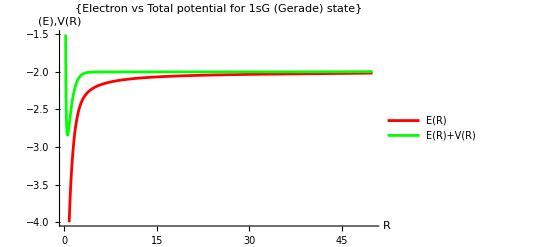

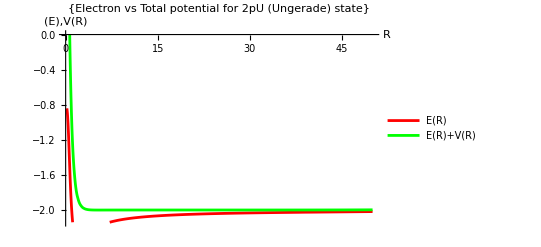

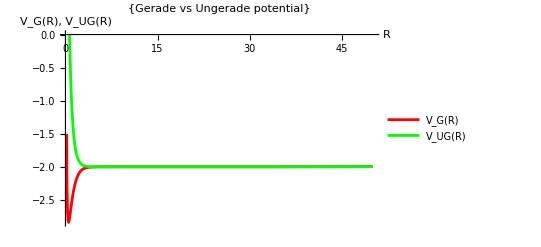

```mathematica
(* Export as above: A, p are constants *)
(* Export to a file so that it can be loaded by other programs *)
Export["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV2.mx",energiesGerade1S, "mx"];
Prepend[energiesUngerade1S, {"R", "E","E+1/r", "A", "p"}];
Export["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV2.mx",energiesUngerade1S, "mx"];

eG = Interpolation[Transpose[{energiesGerade1S[[All,1]],energiesGerade1S[[All,2]]}]];
eGTotal = Interpolation[Transpose[{energiesGerade1S[[All,1]],energiesGerade1S[[All,3]]}]];


Plot[{eG[x],eGTotal[x]},{x,.2,50}, PlotStyle->{Red,Green}, AxesLabel->{"R", "(E),V(R)"}, AxesOrigin->{0,0},PlotLabel->{"Electron vs Total potential for 1sG (Gerade) state"},
PlotRange->{0,-4},PlotLegends->{"E(R)","E(R)+V(R)","egFar"}]


eU = Interpolation[Transpose[{energiesUngerade1S[[All,1]],energiesUngerade1S[[All,2]]}], InterpolationOrder->3];
eUTotal = Interpolation[Transpose[{energiesUngerade1S[[All,1]],energiesUngerade1S[[All,3]]}], InterpolationOrder->3];

Plot[{eU[x],eUTotal[x]},{x,0.2,50}, PlotStyle->{Red,Green}, AxesLabel->{"R", "(E),V(R)"}, AxesOrigin->{0,0},PlotLabel->{"Electron vs Total potential for 2pU (Ungerade) state"}, PlotLegends->{"E(R)","E(R)+V(R)"}]

Plot[{eGTotal[x],eUTotal[x]},{x,0.2,50}, PlotStyle->{Red,Green}, AxesLabel->{"R", "V_G(R), V_UG(R)"}, AxesOrigin->{0,0},PlotRange->{0,-3},PlotLabel->{"Gerade vs Ungerade potential"}, PlotLegends->{"V_G(R)","V_UG(R)"}]
```